```mathematica
Remove["Global`*"]
```

So the Changing solar declination...

```mathematica
δ[n_]:=-ArcSin[.39779 Cos[(.98565(n+0)+1.914 Sin[.98565(n-2)Degree])Degree]]/Degree
approxδ[n_]:=-23.44 Cos[360/365.24(n+0) Degree]
```

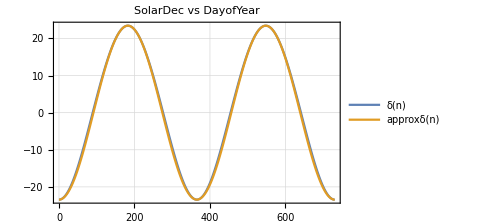

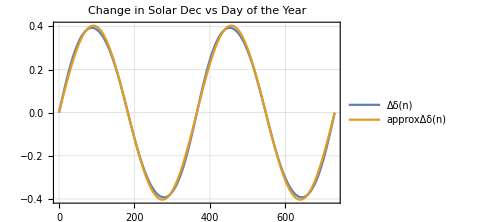

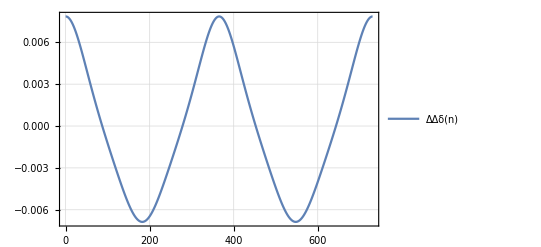

```mathematica
Plot[{δ[n],approxδ[n]},{n,0,365.24*2},PlotPoints->500,PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"SolarDec vs DayofYear"]
(*The change in dec can be measured easily in lab, so lets look at that too*)
Δδ[n_]=D[δ[n],n];
approxΔδ[n_]=D[approxδ[n],n];
Plot[{Δδ[n],approxΔδ[n]},{n,0,365.24*2},PlotPoints->500,PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Change in Solar Dec vs Day of the Year"]
ΔΔδ[n_]=D[Δδ[n],n];
Plot[ΔΔδ[n],{n,0,365.24*2},PlotPoints->500,PlotTheme->"Detailed"]
```

There is an approximation for δ[n], with just cosine. Let’s check and see if it’s right

a Cos[(2 π (n+ϕn))/Pn]

{a→-23.491,Pn→371.837,ϕn→3.29642}

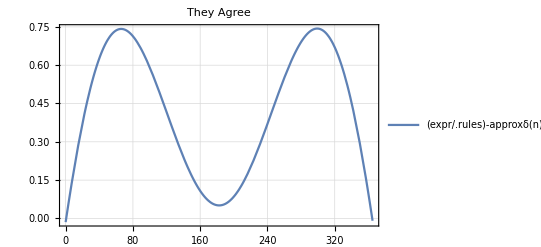

```mathematica
t=Table[{n,δ[n]},{n,0,365,.01}];
expr=a Cos[(2π)/Pn(n +ϕn)]
rules=NonlinearModelFit[t,expr,{{a,23},{Pn,360},{ϕn,0}},n,Method->"LevenbergMarquardt"]["BestFitParameters"]
Plot[{(expr/.rules)-approxδ[n]},{n,0,365},PlotTheme->"Detailed",PlotLabel->"They Agree"]
```

Now lets look at the what is left over after removing the 1 year variation in solar declination, and see what periods pop out

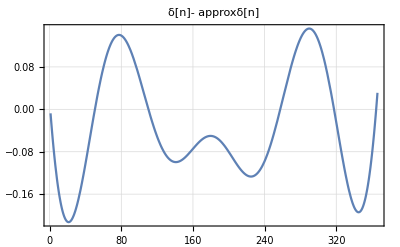

N days x 10 | Power
2 | 704.869
3661 | 704.869

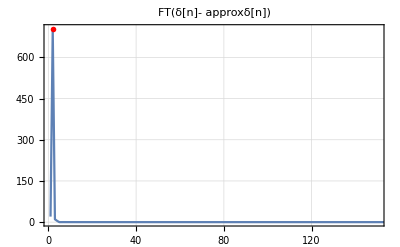

```mathematica
(*Get our table of differences, easier to FT, use .1 day spacing*)
stab=Table[δ[n]-approxδ[n],{n,0,366,.1}]; (*without year variation*)
tab=Table[δ[n],{n,0,366,.1}]; (*with year variation*)
ftt=Fourier[tab]; (*take discrete fourier transform*)
peaks=FindPeaks[Abs[ftt]];(*locate peaks*)

Plot[δ[n]-expr/.rules,{n,1,366},PlotRange->All,PlotTheme->"Detailed",PlotLabel->"δ[n]- approxδ[n]",PlotLegends->None]
TableForm[peaks,TableHeadings->{None,{"N days x 10","Power"}}]
ListLinePlot[{Abs[ftt]},PlotRange->{{1,150},All},PlotTheme->"Detailed",PlotLabel->"FT(δ[n]- approxδ[n])",Epilog->{Red,PointSize[.01],Point[peaks]}]
```